```mathematica
(* Sets the Base directory, changing which files are easiest to acces. *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns","18-03-18_100mTorrBGP","data"}];
If[SystemInformation["Kernel","OperatingSystem"]=="Unix",
folder=FileNameJoin[{"/","home","karl",dropBoxOn}]; ,(* Home coputer is Linux, so needs "/" at beginning *)
folder=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"*)
];

(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{folder}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=Length[directories],i>0,i--,
Print[i -> directories[[i]]];]
(* set rootFolder to the folder name containing the desired Files *)
rootFolder=FileNameJoin[{dataFolder}];
SetDirectory[rootFolder];
(* Obtain the filenames of the excitation functions and print them out.*)
SetDirectory[FileNameJoin[{folder}]];
files=FileNames["EX*.dat"]
```

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-03-18_100mTorrBGP\data

{EX2018-03-18_021149.dat,EX2018-03-18_021318.dat,EX2018-03-18_042007.dat,EX2018-03-18_052845.dat,EX2018-03-18_064305.dat,EX2018-03-18_075144.dat,EX2018-03-18_090558.dat,EX2018-03-18_101436.dat,EX2018-03-18_112902.dat,EX2018-03-18_130418.dat,EX2018-03-18_154743.dat,EX2018-03-18_170735.dat,EX2018-03-18_181617.dat,EX2018-03-18_193116.dat,EX2018-03-18_204001.dat,EX2018-03-18_215513.dat,EX2018-03-18_230359.dat,EX2018-03-19_001900.dat,EX2018-03-19_004104.dat,EX2018-03-19_015629.dat,EX2018-03-19_030510.dat,EX2018-03-19_042024.dat,EX2018-03-19_052911.dat,EX2018-03-19_064414.dat,EX2018-03-19_075259.dat,EX2018-03-19_090755.dat,EX2018-03-19_101639.dat,EX2018-03-19_105809.dat,EX2018-03-19_110123.dat,EX2018-03-19_110504.dat,EX2018-03-19_110857.dat,EX2018-03-19_120957.dat,EX2018-03-19_121428.dat,EX2018-03-19_121708.dat,EX2018-03-19_123813.dat,EX2018-03-19_131949.dat,EX2018-03-19_145937.dat,EX2018-03-19_161426.dat,EX2018-03-19_175336.dat,EX2018-03-19_190822.dat,EX2018-03-19_202907.dat,EX2018-03-19_214353.dat,EX2018-03-19_221055.dat,EX2018-03-19_221259.dat,EX2018-03-19_234036.dat,EX2018-03-20_003227.dat,EX2018-03-20_015230.dat,EX2018-03-20_024420.dat,EX2018-03-20_040433.dat,EX2018-03-20_045630.dat,EX2018-03-20_061643.dat,EX2018-03-20_070837.dat,EX2018-03-20_082845.dat,EX2018-03-20_092043.dat,EX2018-03-20_104044.dat,EX2018-03-20_113237.dat,EX2018-03-20_125251.dat,EX2018-03-20_134446.dat,EX2018-03-20_173918.dat,EX2018-03-20_174314.dat,EX2018-03-20_190651.dat,EX2018-03-20_195846.dat,EX2018-03-20_211910.dat,EX2018-03-20_221123.dat,EX2018-03-20_233146.dat,EX2018-03-21_002337.dat,EX2018-03-21_014405.dat,EX2018-03-21_023606.dat,EX2018-03-21_035623.dat,EX2018-03-21_044819.dat,EX2018-03-21_060839.dat,EX2018-03-21_070036.dat,EX2018-03-21_082110.dat,EX2018-03-21_091308.dat,EX2018-03-21_103336.dat,EX2018-03-21_131018.dat,EX2018-03-21_132814.dat,EX2018-03-21_134126.dat,EX2018-03-21_134407.dat}

## Performs Gaussian Analysis of Excitation Function (both with counts and current)

```mathematica
timeString="203423";
data=ExcitationFunctionProcessor[timeString];
info=<|data["Filename"]->data|>;
timeString="233539";
data=ExcitationFunctionProcessor[timeString];
AppendTo[info,<|data["Filename"]->data|>];
Dataset[info]
```

Dataset[<>]

## Prints out the comments from all of the file names.

```mathematica
For[i=1,i≤Length[files],i++,
comments=GetFileHeaderInfo[files[[i]]]["#Comments:"];
Print[files[[i]]<>" -> "<>comments];
];
```

EX2018-02-13_013554.dat -> does it work here?

EX2018-02-13_014854.dat -> Script Test for exFn and electron pol., temp=100, run=1

EX2018-02-13_023109.dat -> Testing to make sure the negative he target is okay.

EX2018-02-13_023357.dat -> One more run to get the RFA piece in

EX2018-02-13_050758.dat -> Extended run, at increasing temps., temp=100, run=1, prelude

EX2018-02-13_170321.dat -> Measuring polarization etc. at the end of the aborted run., temp=100, run=1, postscript

EX2018-02-13_173556.dat -> Primary increase in current came from adjusting sweep potential

EX2018-02-13_174047.dat -> RFA

EX2018-02-13_182224.dat -> Faster extended data run, temp=105, prelude

EX2018-02-13_230939.dat -> Faster extended data run, temp=105, postscript

EX2018-02-13_233300.dat -> Faster extended data run, temp=110, prelude

EX2018-02-14_042016.dat -> Faster extended data run, temp=110, postscript

EX2018-02-14_044342.dat -> Faster extended data run, temp=115, prelude

EX2018-02-14_093056.dat -> Faster extended data run, temp=115, postscript

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 2 in EX2018-02-14_113518.dat -> <>Missing[KeyAbsent,#Comments:].

EX2018-02-14_113518.dat -> <>Missing[KeyAbsent,#Comments:]

EX2018-02-14_120100.dat -> Dark Counts Background (He just turned off, deflector preventing electrons from reaching target, room lights on, now probe beam is unblocked., temp=100, prelude

EX2018-02-14_131606.dat -> Moly Counts Background (He off, room lights on), temp=100, prelude

EX2018-02-14_141849.dat -> Moly Counts Background (He off, room lights on), rerun- i suspect residual helium in the chamber on the previous run, temp=100, prelude

EX2018-02-14_162159.dat -> Current is fairly unstable, but the polarization numbers are good., temp=115, prelude

EX2018-02-14_192323.dat -> Current is fairly unstable, but the polarization numbers are good., temp=115, postscript

EX2018-02-14_203423.dat -> Current is fairly unstable, but the polarization numbers are good., temp=120, prelude

EX2018-02-14_233539.dat -> Current is fairly unstable, but the polarization numbers are good., temp=120, postscript

## Shows Graphs for the normalization process of the excitation function

{2064.76,2112.08,2067.81,2034.99,2032.7,2022.01,2025.07,2025.07,2051.78,2086.13,2060.94,2022.01,2006.75,2075.45,2047.97,2038.04,2025.83,2007.51,1993.01,1916.68,1905.23,1882.33,1902.94,1839.58,1857.9,1854.85,1799.13,1737.3,1705.24,1711.35,1673.94,1646.46,1607.54,1569.37,1544.94,1477.77,1453.35,1412.89,1377.78,1331.98,1303.74}

{9.36671,9.34576,9.59953,9.83887,9.85635,9.99748,9.96657,9.98928,9.88751,9.69546,9.78631,9.97423,10.083,9.70392,9.7267,9.6215,9.30384,8.9215,8.08124,6.06622,2.70256,0.454224,0.225441,0.190804,0.15609,0.12346,0.122281,0.123755,0.116699,0.130891,0.150543,0.166418,0.11135,0.0605338,0.0323637,0.0223309,0.0123852,0.018402,0.0225,0.0195198,0.0184086}

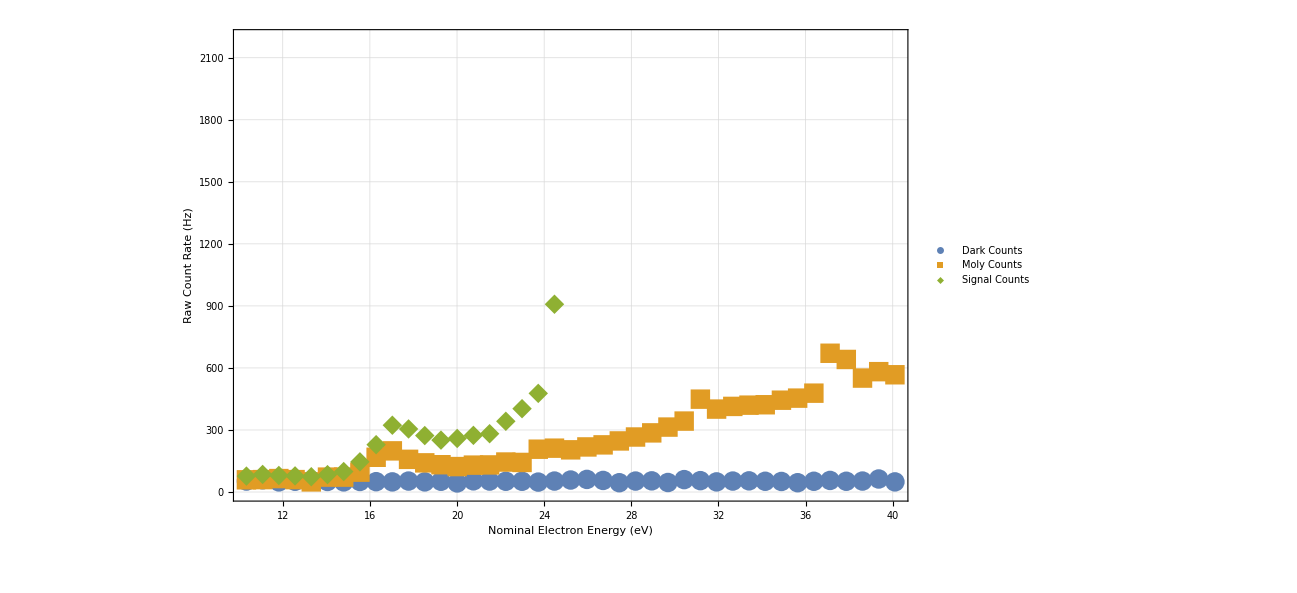

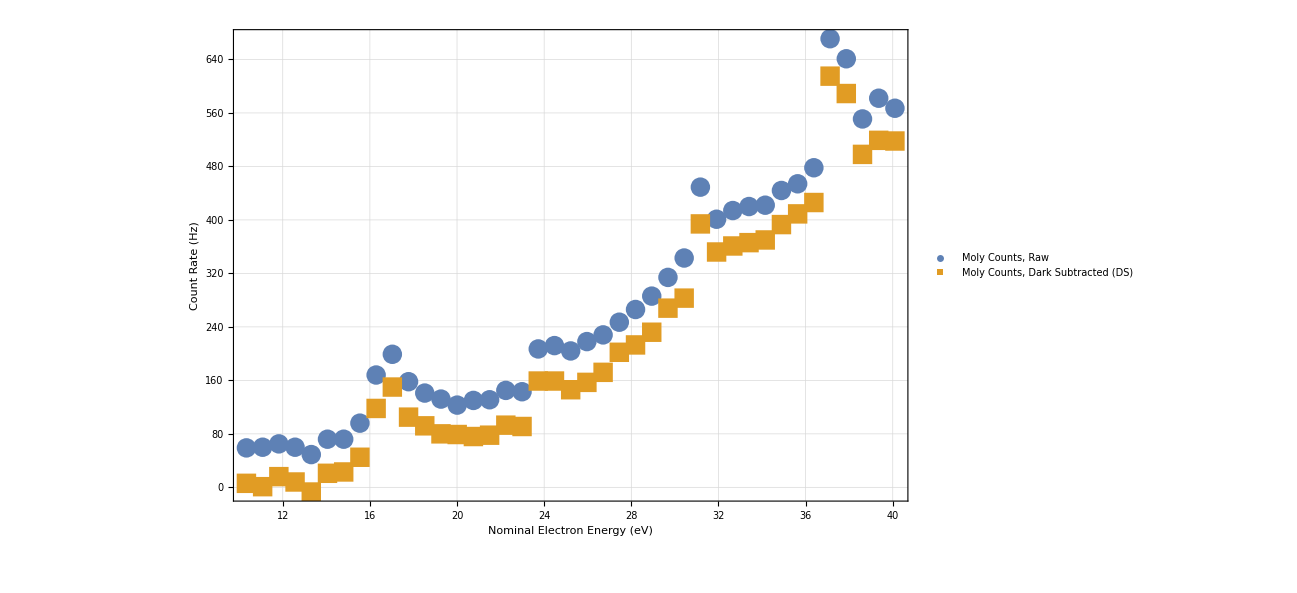

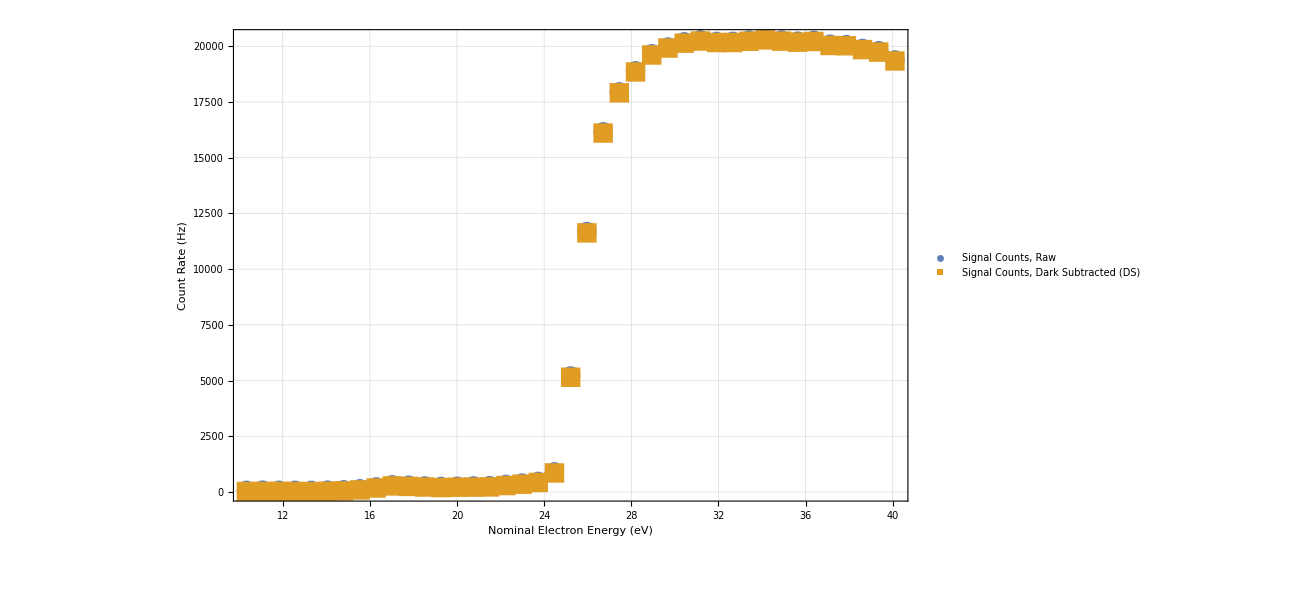

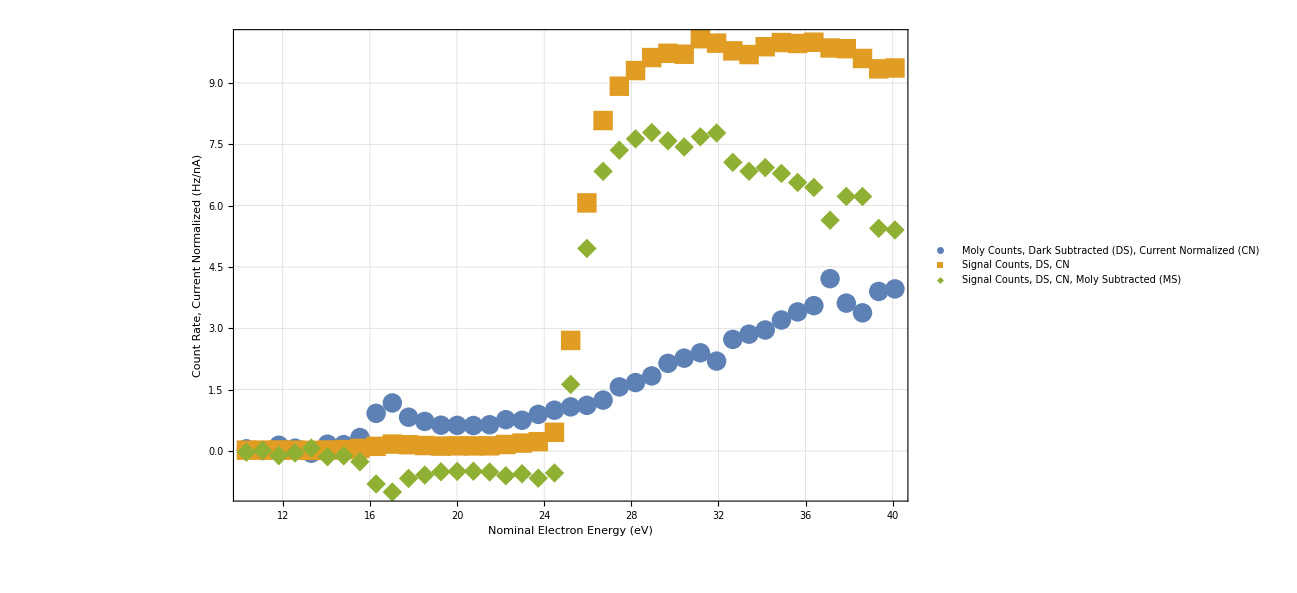

1.60192

1.30091

{{40.1,4.95797},{39.3558,4.99506},{38.6117,5.7085},{37.8675,5.71006},{37.1234,5.17695},{36.3792,5.91222},{35.635,6.02428},{34.8909,6.22698},{34.1467,6.358},{33.4025,6.27554},{32.6584,6.47602},{31.9142,7.13518},{31.17,7.04909},{30.4259,6.82155},{29.6817,6.95877},{28.9376,7.14445},{28.1934,7.00239},{27.4492,6.74843},{26.7051,6.27411},{25.9609,4.54346},{25.2167,1.49158},{24.4726,-0.495991},{23.7284,-0.612973},{22.9843,-0.512618},{22.2401,-0.557158},{21.4959,-0.473618},{20.7518,-0.456624},{20.0076,-0.459699},{19.2634,-0.469461},{18.5193,-0.542165},{17.7751,-0.617487},{17.0309,-0.922953},{16.2868,-0.741188},{15.5426,-0.244292},{14.7985,-0.110754},{14.0543,-0.130245},{13.3101,0.0630734},{12.566,-0.0447064},{11.8218,-0.105908},{11.0776,0.0100458},{10.3335,-0.0299147}}

```mathematica
dataFolderDate="18-02-13";
darkTimeStamp="120100";
darkData=GetFileDataset[files[[GetIndexOfFilenameFromTimestamp[files,darkTimeStamp]]]];
darkHeader=GetFileHeaderInfo[files[[GetIndexOfFilenameFromTimestamp[files,darkTimeStamp]]]];

molyTimeStamp="141849";
molyData=GetFileDataset[files[[GetIndexOfFilenameFromTimestamp[files,molyTimeStamp]]]];
molyHeader=GetFileHeaderInfo[files[[GetIndexOfFilenameFromTimestamp[files,molyTimeStamp]]]];

signalTimeStamp="192323";
signalData=GetFileDataset[files[[GetIndexOfFilenameFromTimestamp[files,signalTimeStamp]]]];
signalHeader=GetFileHeaderInfo[files[[GetIndexOfFilenameFromTimestamp[files,signalTimeStamp]]]];

energyOffset=0;
nA=1*10^-9;
torrTomTorr=1000;
darkCounts=Normal[darkData[All,{"SecondaryElectronEnergy","CountRate","Current"}][All,Values]];
energyArray=Transpose[darkCounts][[1]]+energyOffset;
darkCountArray=Transpose[darkCounts][[2]];

molyCounts=Normal[molyData[All,{"SecondaryElectronEnergy","CountRate","Current"}][All,Values]];
molyCountArray=Transpose[molyCounts][[2]];
molyCurrentMag=molyHeader["#MagnitudeOfCurrent(*10^-X):"];
molyCurrentArrayNa=Transpose[molyCounts][[3]]*10^(-molyCurrentMag)/nA;
ListPlot[{Transpose[{energyArray,darkCountArray}],Transpose[{energyArray,molyCountArray}]}];
molyDarkSubtracted=molyCountArray-darkCountArray;
molyCurrentNorm=molyDarkSubtracted/molyCurrentArrayNa;

signalCounts=Normal[signalData[All,{"SecondaryElectronEnergy","CountRate","Current"}][All,Values]];
signalCountArray=Transpose[signalCounts][[2]];
signalEnergyArray=Transpose[signalCounts][[1]]+energyOffset;
signalCurrentMag=signalHeader["#MagnitudeOfCurrent(*10^-X):"];
signalCurrentArrayNa=Transpose[signalCounts][[3]]*10^(-signalCurrentMag)/nA
signalDarkSubtracted=signalCountArray-Take[darkCountArray,{1,Length[signalCountArray]}];
signalCurrentNorm=signalDarkSubtracted/signalCurrentArrayNa
signalMolySubtracted=signalCurrentNorm-Take[molyCurrentNorm,{1,Length[signalCountArray]}];
signalHeNorm=signalMolySubtracted/(signalHeader["#CVGauge(He)(Torr):"]*torrTomTorr);

xAxisLabel="Nominal Electron\nEnergy (eV)";
yAxisLabel="Raw Count Rate (Hz)";
rawCountsPlot=ListPlot[{Legended[Drop[darkCounts,None,{-1}],"Dark Counts"],Legended[Drop[molyCounts,None,{-1}],"Moly Counts"],Legended[Drop[signalCounts,None,{-1}],"Signal Counts"]},AxesLabel->{xAxisLabel,yAxisLabel},GridLines->Automatic]

yAxisLabel="Count Rate (Hz)";
molyCountsPlot=ListPlot[{Legended[Transpose[{energyArray,molyCountArray}],"Moly Counts, Raw"],Legended[Transpose[{energyArray,molyDarkSubtracted}],"Moly Counts, Dark Subtracted (DS)"]},AxesLabel->{xAxisLabel,yAxisLabel}]

yAxisLabel="Count Rate (Hz)";
signalCountsPlot=ListPlot[{Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalCountArray}],"Signal Counts, Raw"],Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalDarkSubtracted}],"Signal Counts, Dark Subtracted (DS)"]},AxesLabel->{xAxisLabel,yAxisLabel}]

yAxisLabel="Count Rate,\nCurrent Normalized (Hz/nA)";
currentNormalizedPlot=ListPlot[{Legended[Transpose[{energyArray,molyCurrentNorm}],"Moly Counts, Dark Subtracted (DS),\nCurrent Normalized (CN)"],Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalCurrentNorm}],"Signal Counts, DS, CN"],
Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalMolySubtracted}],"Signal Counts, DS, CN, Moly Subtracted (MS)"]
},AxesLabel->{xAxisLabel,yAxisLabel}]

Mean[molyCurrentNorm]
StandardDeviation[molyCurrentNorm]

fullyNormalizedExcitationFunction=Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalHeNorm}]

Export[dataFolderDate<>"_exFnRawCounts.png",rawCountsPlot,ImageResolution->200];
Export[dataFolderDate<>"_exFnMolyCounts.png",molyCountsPlot,ImageResolution->200];
Export[dataFolderDate<>"_exFnSignalCounts.png",signalCountsPlot,ImageResolution->200];
Export[dataFolderDate<>"_exFnCurrentNormalized.png",currentNormalizedPlot,ImageResolution->200];
```

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large,PlotStyle->{Automatic,20},LabelStyle->27,GridLines->Automatic];
SetOptions[ListPlot,BaseStyle->{FontSize->24},ImageSize->Large,PlotMarkers->{Automatic,20},LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];

plotLabel="Plot Label";
yAxisLabel="Y";
xAxisLabel="X";
ps={LabelStyle->18,PlotLabel->plotLabel,AxesLabel->{xAxisLabel,yAxisLabel}}

GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];

GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,rawFile[[k]][[1]]->joinedWithSpaces];
,
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];

GaussianAnalyzer[timeString_,dependentVariableString_]:=Module[{fitInfo, bothPlot, derivativePlot,entry,file,ps,header,data,energy,energyDiff,depVar,depVarDiff,energyOneRemoved,depVarDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,dataLabel1,dataLabel2,x1,y1,offset, new23,plot,derPlot,index},
index=GetIndexOfFilenameFromTimestamp[files,timeString];
file=files[[index]];
entry=<||>;

header=GetFileHeaderInfo[file];
data=GetFileDataset[file];
energy=Reverse[Normal[data[All,"SecondaryElectronEnergy"]]];
depVar=Reverse[Normal[data[All,dependentVariableString]]];
depVarDiff=Differences[depVar];
energyDiff=Differences[energy];
energyOneRemoved=Take[energy,{1,-2}];
depVarDer=depVarDiff/energyDiff;
plot=ListPlot[Transpose[{energy,depVar}],PlotLabel->dependentVariableString<>" vs. Energy: "<>timeString,FrameLabel->{"'Slow' Electron Energy (eV)",dependentVariableString},Frame->True];
derPlot=ListPlot[Transpose[{energyOneRemoved,depVarDer}],PlotLabel->dependentVariableString<>" Derivative\nvs. Energy: "<>timeString,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"},Frame->True];


plotTitle="Gaussian Analysis";

plotData=Transpose[{energy,depVar}];
plotData2=Transpose[{energyOneRemoved,depVarDer}];


(*
yAxisTitle="d(Counts)/d(Energy)";
xAxisTitle="Electron Energy (eV)";
*)
dataLabel1="Data";
dataLabel2="Derivative";

ps={ImageSize->Large, PlotLabel->plotTitle,AxesLabel->{"X","Y"}};

plotData=plotData2;
gaussModel[x_]=ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
(*Find the position of the peak of the derivative data*)
maxDerPos=Position[depVarDer,Max[depVarDer]][[1]];
energyOfPeak=energyOneRemoved[[maxDerPos]][[1]];

fit=NonlinearModelFit[plotData,gaussModel[x],{ampl,{m,energyOfPeak},{σ,.9}},x];
model=Normal[fit];
pe=fit["BestFitParameters"]; (*Parameter Estimates*)
errors=fit["ParameterErrors"];

new23=m-(2*Sqrt[2Log[10]]σ)/2/.pe;
offset=23-new23;



x1=energyOfPeak-(3σ/.pe);
y1=.25*(ampl)/.pe;
fitInfo=StringForm["μ=``± ``\nσ=``±``",NumberForm[m/.pe,3],NumberForm[errors[[2]],1],NumberForm[σ/.pe,3],NumberForm[errors[[3]],1]];
(*Print[Show[{Plot[gaussModel[x]/.pe,{x,energyOfPeak-5,energyOfPeak+5},PlotRange->All,PlotLabel->"Gaussian Fit To Derivative\nof "<>dependentVariableString<>" Analysis: "<> timeString,Frame->True,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"}],
Graphics[Text[fitInfo,{x1,y1}],BaseStyle->15],
ListPlot[plotData,PlotLabel->"PLOT2"]}]];*)
bothPlot=ListPlot[{Legended[plotData,dataLabel2],Legended[plotData2,dataLabel1]}];
derivativePlot=ListPlot[Legended[plotData2,dataLabel2],ps];

AppendTo[entry,header];
AppendTo[entry,<|dependentVariableString<>"plot"->plot,"N2Offset"-> data[1,"N2Offset"],"filBias"-> data[1,"bias"],dependentVariableString<>"onsetEnergy"-> m/.pe,dependentVariableString<>"onsetWidth"->  σ/.pe,dependentVariableString<>"lowEnergySignal"-> depVar[[1]],dependentVariableString<>"highEnergySignal"-> depVar[[-1]]|>];
entry
];

ExcitationFunctionProcessor[timeString_]:=Module[{file,ps,header,data,energy,energyDiff,current,currentDiff,energyOneRemoved,currentDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,x1,y1,return},
return=<||>;
AppendTo[return,GaussianAnalyzer[timeString,"CountRate"]];
AppendTo[return,GaussianAnalyzer[timeString,"Current"]];
return
];

GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];

GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"-> "",":"->""}]->joinedWithSpaces];
,
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"->"",":"->""}]->rawFile[[k]][[2]]];
];
k++;
];
association
];
```